```mathematica
Interpolate[data_, iδ_]:=Module[{},
	rdf = Flatten[Table[{{(is10-1)*iδ, (iη-1)*iδ}, data[[is10, iη]]}, {is10, 1, Length[data]}, {iη, 1, Length[data]}],1];
	Interpolation[rdf, InterpolationOrder->3]
];

InterpolateNoCutoff[data_, iδ_, ηmax_]:=Module[{},
rdf = Flatten[Table[{{(is10-1)*iδ , (iη-1)*iδ}, Piecewise[{{data[[is10- iη + Length[data], iη]], iη - Length[data]< is10 < iη}}, 1]}, {is10, -Length[data], Length[data]}, {iη, 1, Length[data]}],1];
	Interpolation[rdf, InterpolationOrder->3]
];
```

```mathematica
(* import data and interpolate *)
inputDir = "/Users/brandonmanley/Desktop/PhD/moment_evolution/evolved_dipoles/largeNc&Nf/d01_ones_rc/";
polAmps =Table[Interpolate[Import[inputDir<>"d01_NcNf3_ones_"<>ia<>"_rc.dat"], 0.01], {ia, {"Q","G2", "I3", "I4", "I5"}}]

(*inputDir = "/Users/brandonmanley/Desktop/PhD/moment_evolution/evolved_dipoles/largeNc&Nf/d05_ones_rc/";
polAmps =Table[InterpolateNoCutoff[Import[inputDir<>"d05_NcNf3_ones_"<>ia<>"_rc.dat"], 0.05, 10], {ia, {"Q","G2", "I3", "I4", "I5"}}];*)
```

{InterpolatingFunction[{{0., 8.}, {0., 8.}}, <>],InterpolatingFunction[{{0., 8.}, {0., 8.}}, <>],InterpolatingFunction[{{0., 8.}, {0., 8.}}, <>],InterpolatingFunction[{{0., 8.}, {0., 8.}}, <>],InterpolatingFunction[{{0., 8.}, {0., 8.}}, <>]}

```mathematica
(*BlendFunc[s10_]:= Log[(1-s10)/1];*)
(*BlendFunc[s10_]:= 1/(1+ Exp[6*s10])-1/2;*)
BlendFunc[s10_]:= 0;
frozenAmp[ s10_,η_, amp_]:= Piecewise[{{amp[s10, η], s10>=0}, {amp[0, η](1+BlendFunc[s10]), s10< 0}}];
doubleBessel[p_, Q_, z_,x_,  Λ_,r_] := r BesselJ[0, p r] BesselK[0,Q  Sqrt[z*(1-z)] r] polAmps[[1]][Sqrt[3/(2π)]Log[1/(r^2 Λ^2)], Sqrt[3/(2π)] Log[Q^2/(x Λ^2)]];
```

```mathematica
diffLams = Table[Table[{p ,NIntegrate[doubleBessel[p, Sqrt[5], 0.4, 0.01, Λ, r], {r,4*10^-2, 1/Λ}]}, {p, 0, 10, 0.1}], {Λ,0.1, 1, 0.1}];
```

```mathematica
Manipulate[ListLogPlot[{diffLams[[i]]/. {x_,y_}:>{x,Abs[y]}}, PlotRange->All, Joined->True, PlotLegends->{"Λ="<>ToString[i/10.0]<> " GeV"}, PlotLabel->"(Q_(00))^(00)(p, z=0.4; Q^2=5, x=0.01)"], {i, 1, Length[diffLams], 1}]
```

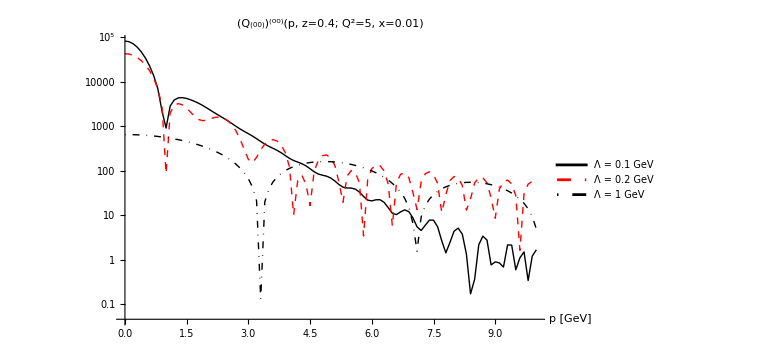

/Users/brandonmanley/Desktop/PhD/dijet_DSA/bmanley/Lambda_var.png

```mathematica
Lplot = ListLogPlot[{diffLams[[1]]/. {x_,y_}:>{x,Abs[y]}, diffLams[[2]]/. {x_,y_}:>{x,Abs[y]}, diffLams[[-1]]/. {x_,y_}:>{x,Abs[y]}}, PlotRange->All, Joined->True, PlotLegends->{"Λ = 0.1 GeV", "Λ = 0.2 GeV", "Λ = 1 GeV"}, PlotLabel->"(Q_(00))^(00)(p, z=0.4; Q^2=5, x=0.01)", PlotStyle->{{Thick, Black}, {Thick, Red, Dashed}, {Thick, Black, DotDashed}}, AxesLabel->{"p [GeV]", ""},
 ImageSize->Large, BaseStyle->{FontFamily->"Times New Roman",FontSize->14},  LabelStyle->{FontFamily->"Times New Roman",FontSize->14}, GridLines->Automatic]
Export["/Users/brandonmanley/Desktop/PhD/dijet_DSA/bmanley/Lambda_var.png", Lplot]
```

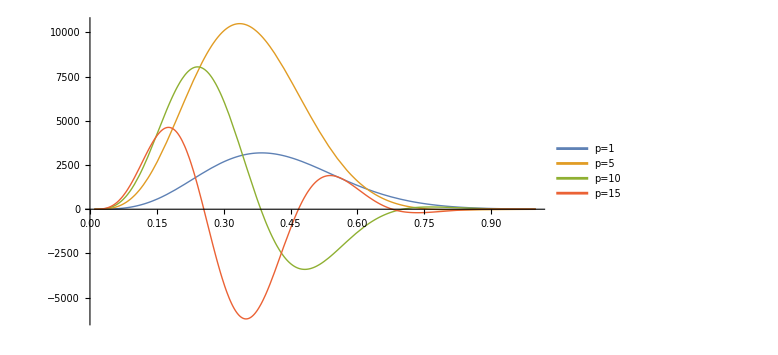

```mathematica
ζ = 10;
Plot[{r BesselJ[1, 1 r] BesselK[1,Q  Sqrt[z*(1-z)] r] polAmps[[1]][Sqrt[3/(2π)]Log[1/r^2], Sqrt[3/(2π)] Log[s]] Exp[-ζ r^2],
r BesselJ[1, 5 r] BesselK[1,Q  Sqrt[z*(1-z)] r] polAmps[[1]][Sqrt[3/(2π)]Log[1/r^2], Sqrt[3/(2π)] Log[s]] Exp[-ζ r^2],
r BesselJ[1, 10 r] BesselK[1,Q  Sqrt[z*(1-z)] r] polAmps[[1]][Sqrt[3/(2π)]Log[1/r^2], Sqrt[3/(2π)] Log[s]] Exp[-ζ r^2],
r BesselJ[1, 15 r] BesselK[1,Q  Sqrt[z*(1-z)] r] polAmps[[1]][Sqrt[3/(2π)]Log[1/r^2], Sqrt[3/(2π)] Log[s]] Exp[-ζ r^2]}
, {r,1/Sqrt[s],1 }, PlotLegends->{"p=1", "p=5", "p=10", "p=15"}, PlotStyle->Thick, ImageSize->Large, BaseStyle->"Subtitle"]
```

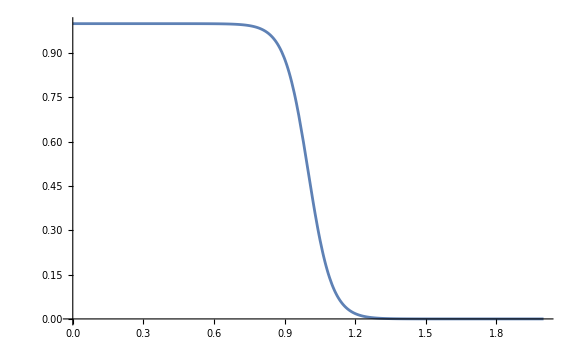

```mathematica
ζ2= 20;
Plot[1/(1+ Exp[ζ2(r - 1)]), {r,0,2}, PlotRange->All, ImageSize->Large]
```

```mathematica
toyDB[p_, Q_, r_, a_, z_]:= r^a BesselJ[0, p r] BesselK[0,Q Sqrt[z(1-z)] r];


Manipulate[Plot[{doubleBessel[p, Sqrt[5], 0.4,0.001, 0.2,r],20000toyDB[p, Sqrt[5], r]},{r,0.01,5}, PlotLegends->{"p=1", "p=5", "p=10", "p=15"}, PlotStyle->Thick, ImageSize->Large, BaseStyle->"Subtitle"], {p, 0,10}]
```

InterpolatingFunction::dmval: Input value {8.57443,8.10949} lies outside the range of data in the interpolating function. Extrapolation will be used.

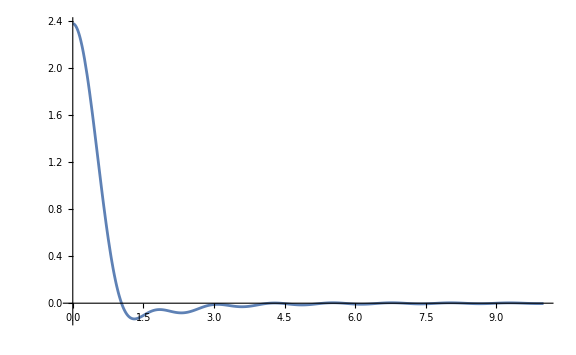

```mathematica
Plot[NIntegrate[r^a BesselJ[0, p r] BesselK[0,Q Sqrt[z(1-z)] r]/.{a->3, Q->Sqrt[5], z->0.4}, {r,0, 1/0.2}], {p,0,10},  PlotRange->All, ImageSize->Large]
```

```mathematica
Solve[Sqrt[z(1-z)]==1, z]
```

{{z→(-1)^(1/3)},{z→-(-1)^(2/3)}}

```mathematica
0.5*0.5
```

0.25